```mathematica
n=Length[λ[[1]]]
```

200

```mathematica
Do[
fileName=ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/output``.txt",a]];λ=ReadList[fileName];Export[ToString[StringForm["/Users/leo/Desktop/ggg/ggg00``.png",a+100]],Graphics[GeometricTransformation[{(**Table[If[FF[x,k]==1,LozS[x+1,k-1,eps],If[x+k>0,LozL[x+1,k-1,eps]]],{k,1,n},{x,-n+1,5n/4-1}]**),Table[LozV[λ[[1]][[i]][[j]]-j,i,eps],{i,1,n},{j,1,i}]},t]],ImageResolution->250],{a,0,40,1}]
```

Part::partw: Part 51 of {{1., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, « 48 », {34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 34., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1., 1.}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Export::nodir: Directory "/Users/leo/Desktop/ggg/" does not exist.

Export::noopen: Cannot open "/Users/leo/Desktop/ggg/ggg00100.png".

$Aborted

```mathematica
fileName=StringForm["/Users/leopetrov/Dropbox/Sci/Glauber_Simulation/output``.txt",a];
```

```mathematica
LozV[x_,y_,eps_]:={EdgeForm[Thickness[eps]],Darker[Gray],Polygon[{{x-1/2,y },{x-1/2,y +1},{x+1/2,y },{x+1/2,y-1},{x-1/2,y }}]}
```

```mathematica
LozV[x_,y_,eps_]:={EdgeForm[Thickness[eps]],RGBColor[70/256,162/256,141/256],Polygon[{{x-1/2,y },{x-1/2,y +1},{x+1/2,y },{x+1/2,y-1},{x-1/2,y }}]}
```

```mathematica
LozL[x_,y_,eps_]:={EdgeForm[Thickness[eps]],RGBColor[249/256,187/256,78/256],Polygon[{{x-1/2,y},{x-3/2,y+1 },{x-1/2,y+1},{x+1/2,y },{x-1/2,y }}]}
```

```mathematica
LozS[x_,y_,eps_]:={EdgeForm[Thickness[eps]],RGBColor[240/256,92/256,80/256],Polygon[{{x-1/2,y},{x-1/2,y+1},{x+1/2,y+1},{x+1/2,y },{x-1/2,y }}]}
```

```mathematica
FF[x_,k_]:=Sum[If[x>=λ[[1]][[k]][[i]]-i,1,0],{i,1,k}]-If[k>1,Sum[If[x>=λ[[1]][[k-1]][[i]]-i,1,0],{i,1,k-1}],0]
```

```mathematica
eps:=0.00015
```

```mathematica
t:={{1,1/2},{0,.85}}
```

```mathematica
Do[
fileName=ToString[StringForm["/Users/leonidpetrov/Dropbox/Sci/Glauber_Simulation/output``.txt",a]];λ=ReadList[fileName];Export[ToString[StringForm["/Users/leonidpetrov/Dropbox/Sci/Glauber_Simulation/agg``.png",a+10]],Graphics[GeometricTransformation[{Table[If[FF[x,k]==1,LozS[x+1,k-1,eps],If[x+k>0,LozL[x+1,k-1,eps]]],{k,1,n},{x,-n+1,n/2-1}],Table[LozV[λ[[1]][[i]][[j]]-j,i,eps],{i,1,n},{j,1,i}]},t]],ImageResolution->1500],{a,501,501}]
```

$Aborted

```mathematica
n=Length[λ[[1]]]
```

400

```mathematica
fileName=ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/output``.txt",5]];
```

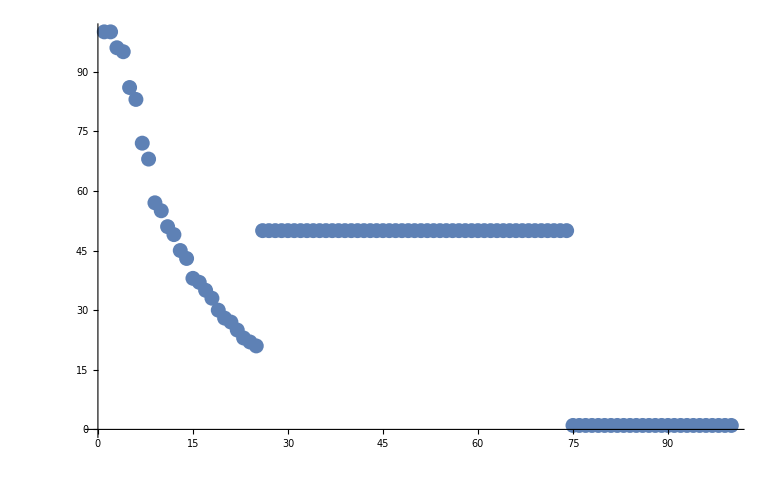

```mathematica
ListPlot[Table[λ[[1]][[n/2]][[i]],{i,1,n/2}]]
```

```mathematica
Do[
fileName=ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/output``.txt",a]];λ=ReadList[fileName];Export[ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/agg``.png",a+10]],Graphics[GeometricTransformation[{{Table[If[FF[x,k]==1,LozS[x+1,k-1,eps],If[x+k>0,LozL[x+1,k-1,eps]]],{k,1,n},{x,-n+1,n/2-1}],Table[LozV[λ[[1]][[i]][[j]]-j,i,eps],{i,1,n},{j,1,i}]},Line[{{1,0},{n/2+1/2,0},{n/2+1/2,0}+n/2{0,1},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2}+{-n/2,0},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2}+{-n/2,0}+{0,-n/2},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2}+{-n/2,0}+{0,-n/2}+{n/2,-n/2}}]},t]],ImageResolution->500],{a,520,527}]
```

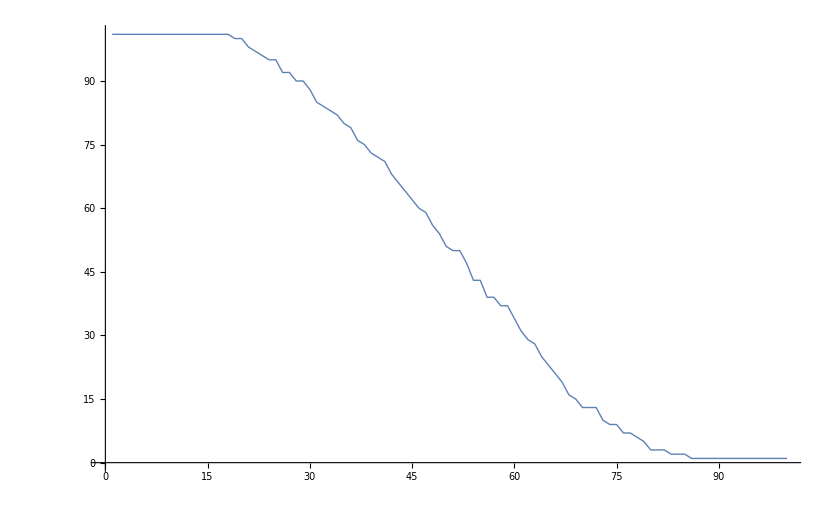

```mathematica
ListLinePlot[Table[λ[[1]][[n/2]][[i]],{i,1,n/2}],PlotRange->Full,PlotStyle->Thick,PlotRange->Full]
```

```mathematica
avg:=Table[0,{i,1,n/2}];count:=0
```

```mathematica
Do[
fileName=ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/output``.txt",a]];λ=ReadList[fileName];avg+=Table[λ[[1]][[n/2]][[i]],{i,1,n/2}];count+=1,{a,400,527}]
```

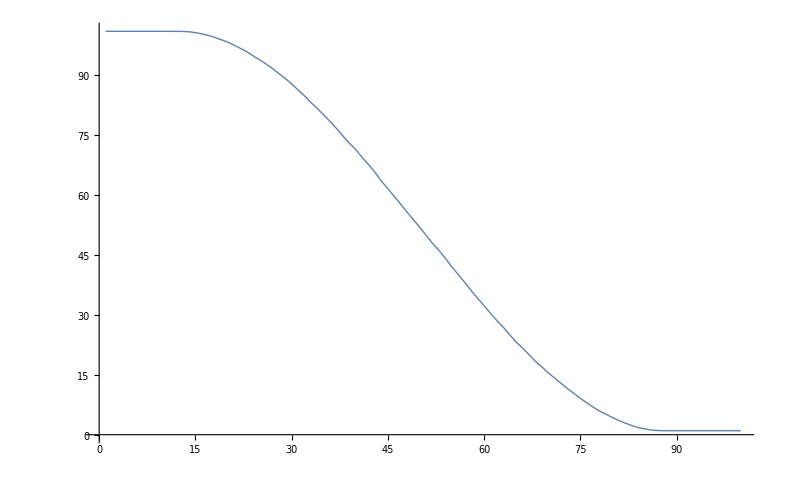

```mathematica
ListLinePlot[avg/count,PlotStyle->Thick]
```

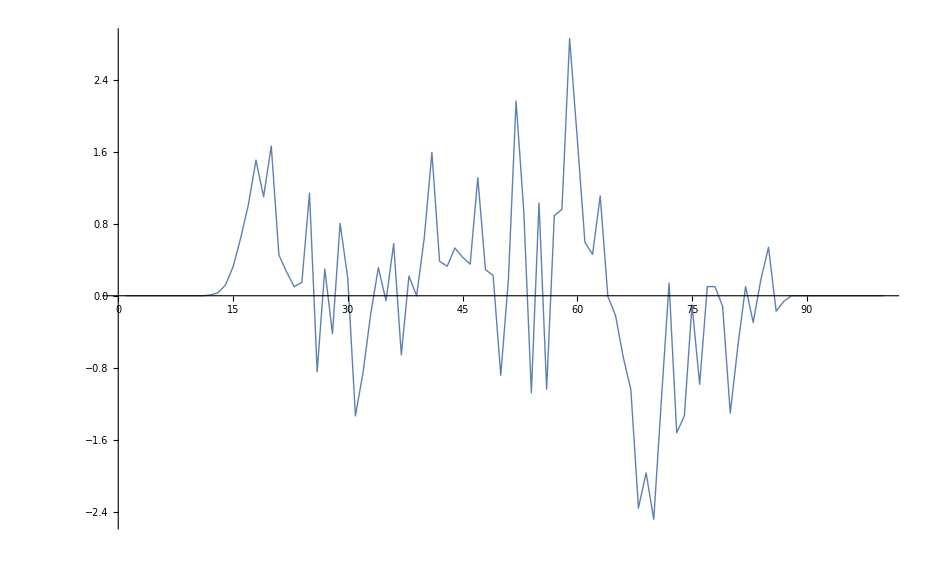

```mathematica
ListLinePlot[Table[λ[[1]][[n/2]][[i]],{i,1,n/2}]-avg/count,PlotRange->Full,PlotStyle->Thick]
```